```mathematica
(*
To meet continuity constraints, need first segment to be quartic,
and second segment to be quintic
*)
```

```mathematica
seg0[r_] := 1 + r*(b + r*(d + r*(f + r*h)))
seg1[r_, wr_] := a + (r-wr)*(c + (r-wr)*(e + (r-wr)*(g + (r-wr)*(i + (r-wr)*j))))
seg0[r]
seg1[r, wr]
```

1+r (b+r (d+r (f+h r)))

a+(c+(e+(g+(i+j (r-wr)) (r-wr)) (r-wr)) (r-wr)) (r-wr)

```mathematica
dseg0[r_] := FullSimplify[D[seg0[rr], rr]] /. {rr->r}
dseg1[r_, wr_] := FullSimplify[D[seg1[rr,wr], rr]] /. {rr->r}
dseg0[r]
dseg1[r,wr]
```

b+r (2 d+r (3 f+4 h r))

c+(r-wr) (2 e+(r-wr) (3 g+(r-wr) (4 i+5 j r-5 j wr)))

```mathematica
ddseg0[r_] := FullSimplify[D[dseg0[rr], rr]] /. {rr->r}
ddseg1[r_, wr_] := FullSimplify[D[dseg1[rr,wr], rr]] /. {rr->r}
ddseg0[r]
ddseg1[r, wr]
```

2 (d+3 r (f+2 h r))

2 (e+(r-wr) (3 g+2 (r-wr) (3 i+5 j r-5 j wr)))

```mathematica
dddseg0[r_] := FullSimplify[D[ddseg0[rr], rr]] /. {rr->r}
dddseg1[r_, wr_] := FullSimplify[D[ddseg1[rr, wr], rr]] /. {rr->r}
dddseg0[r]
dddseg1[r, wr]
```

6 (f+4 h r)

6 (g+2 (2 i+5 j (r-wr)) (r-wr))

```mathematica
(* we want C^3 continuity everywhere except at r=0 *)
coeffs[wr_, wd_] := Solve[{ 
seg0[wr] == wd, seg1[wr,wr] == wd,seg1[1,wr] == 0,
dseg0[wr] == 0, dseg1[wr, wr] == 0,dseg1[1,wr] == 0,
ddseg0[wr] == ddseg1[wr,wr], ddseg1[1,wr] == 0 ,
dddseg0[wr] == dddseg1[wr,wr], dddseg1[1,wr] == 0 
},
{a, b,c,d,e,f,g, h, i, j}][[1]]
coeffs[wr, wd]
```

{a→wd,b→(4 (1-wd-3 wr+3 wd wr+3 wr^2+2 wd wr^2-wr^3+wd wr^3))/((-1+wr)^3 wr),c→0,d→-(2 (3-3 wd-9 wr+9 wd wr+9 wr^2+16 wd wr^2-3 wr^3+8 wd wr^3))/((-1+wr)^3 wr^2),e→-(10 wd)/(-1+wr)^2,f→(4 (1-wd-3 wr+3 wd wr+3 wr^2+7 wd wr^2-wr^3+6 wd wr^3))/((-1+wr)^3 wr^3),g→-(20 wd)/(-1+wr)^3,h→-(1-wd-3 wr+3 wd wr+3 wr^2+7 wd wr^2-wr^3+11 wd wr^3)/((-1+wr)^3 wr^4),i→-(15 wd)/(-1+wr)^4,j→-(4 wd)/(-1+wr)^5}

```mathematica
well[r_, wr_, wd_] := If [r< wr,
seg0[r] /. coeffs[wr,wd],
If [r < 1,
seg1[r,wr] /. coeffs[wr,wd],
0]]
dwell[r_, wr_, wd_] := If [r< wr,
dseg0[r] /. coeffs[wr,wd],
If [r < 1,
dseg1[r,wr] /. coeffs[wr,wd],
0]]
ddwell[r_, wr_, wd_] := If [r< wr,
ddseg0[r] /. coeffs[wr,wd],
If [r < 1,
ddseg1[r,wr] /. coeffs[wr,wd],
0]]
dddwell[r_, wr_, wd_] := If [r< wr,
dddseg0[r] /. coeffs[wr,wd],
If [r < 1,
dddseg1[r,wr] /. coeffs[wr,wd],
0]]
```

```mathematica
wellRad = 0.666
wellDepth = -0.005
```

0.666

-0.005

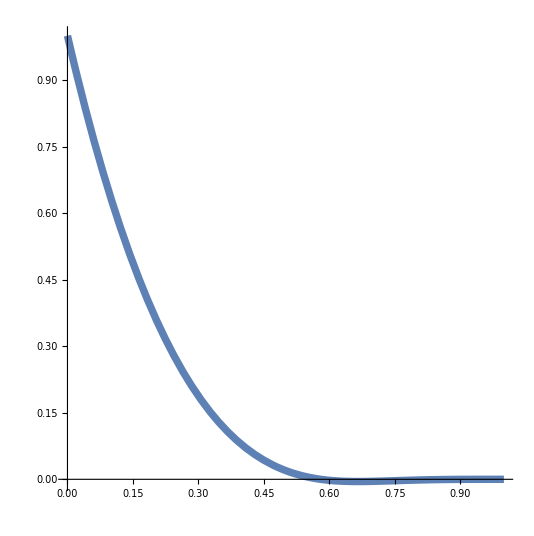

```mathematica
Plot[well[r, wellRad,wellDepth], {r,0,1}, PlotRange->All, PlotStyle->Thickness[0.01], AspectRatio->Automatic]
```

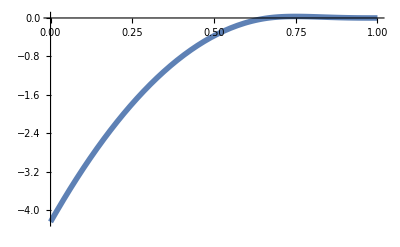

```mathematica
Plot[dwell[r,wellRad,wellDepth], {r,0,1}, PlotRange->All, PlotStyle->Thickness[0.01]]
```

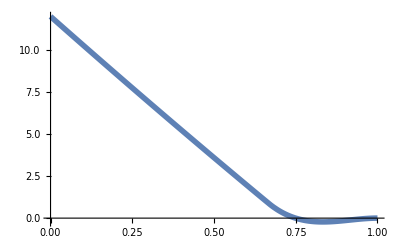

```mathematica
Plot[ddwell[r, wellRad,wellDepth], {r,0,1}, PlotRange->All, PlotStyle->Thickness[0.01]]
```

```mathematica
CForm[N[seg0[r] /. coeffs[wellRad,wellDepth], 10]]
```

1. + r*(-4.248582222661734 + r*(5.991287388535527 + (-2.864766048887071 + 0.06790595504541913*r)*r))

```mathematica
CForm[N[seg1[r,wellRad] /. coeffs[wellRad,wellDepth], 10]]
```

-0.005 + (-5.28862880397578e-16 + (0.4482053856358993 + 
         (-2.6838645846460842 + (6.026642031390917 - 4.811690244623482*(-0.666 + r))*(-0.666 + r))*(-0.666 + r))*
       (-0.666 + r))*(-0.666 + r)

```mathematica
CForm[N[dseg0[r] /. coeffs[wellRad,wellDepth], 10]]
```

-4.248582222661734 + r*(11.982574777071054 + (-8.594298146661213 + 0.2716238201816765*r)*r)

```mathematica
CForm[N[dseg1[r,wellRad] /. coeffs[wellRad,wellDepth], 10]]
```

-15.42591894092919 + 0.4482053856358993*(-1.332 + 2.*r) + 
   r*(-2.6838645846460842*(-3.9960000000000004 + 3.*r) + 
      6.026642031390917*(5.322672000000001 + r*(-7.992000000000001 + 4.*r)) - 
      4.811690244623482*(-5.908165920000002 + r*(13.306680000000002 + r*(-13.32 + 5.*r))))